```mathematica
ClearAll["Global1*"]
```

```mathematica
F:={{F11,F12,F13},{F21,F22,F23},{F31,F32,F33}}
```

```mathematica
(*R:=RotationMatrix[π,{1,-1,0}]
R:=RotationMatrix[π,{1,1,0}]
R:=IdentityMatrix[3]
R:=RotationMatrix[-π/2,{0,0,1}]
R:=RotationMatrix[π/2,{0,0,1}]
R:=RotationMatrix[π,{1,0,0}]
R:=RotationMatrix[π,{0,1,0}]
R:=RotationMatrix[π,{0,0,1}]
*)
R:=RotationMatrix[π,{0,0,1}]
R.F.Transpose[R]//MatrixForm
R.{1,0,0}
Transpose[R.{1,0,0}].R.F.Transpose[R].R.{1,0,0}
```

(F11 | F12 | -F13
F21 | F22 | -F23
-F31 | -F32 | F33)

{-1,0,0}

F11

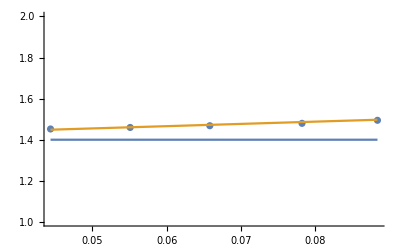

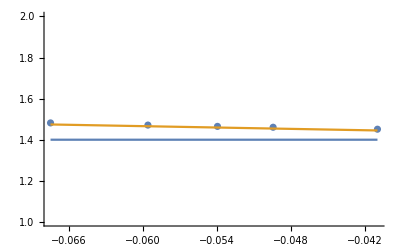

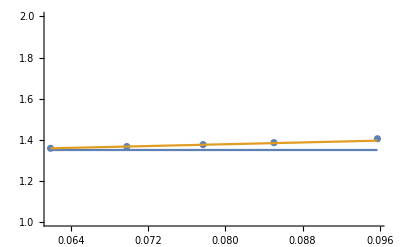

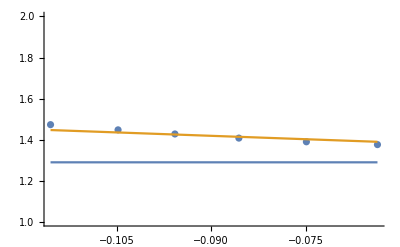

```mathematica
(*We extract data from the two curves below. 
-Graphics-
The data is stores in ϵ vs Subscript[T, c] for T(ension) (sample)1
*)
EpsVsTcForT1:={{0.044350282485875636,1.4522703273495248},{0.05508474576271183,1.459662090813094},{0.06581920903954797,1.4681098204857443},{0.07824858757062142,1.4797254487856388},{0.08841807909604515,1.4945089757127772}}
TcT1=Range[Length[EpsVsTcForT1]];
ϵT1=Range[Length[EpsVsTcForT1]];
For[i=1,i<=Length[EpsVsTcForT1],i++,TcT1[[i]]=EpsVsTcForT1[[i]][[2]];ϵT1[[i]]=EpsVsTcForT1[[i]][[1]]]
{Length[TcT1],Length[ϵT1]};
TcT1;
ϵT1;
pltT11=ListPlot[Transpose@{ϵT1,TcT1}];(*Cp vs temp*)
pltT12=Plot[{1.4,1.1x+1.4},{x,ϵT1[[1]],ϵT1[[Length[ϵT1]]]}];
Show[pltT11,pltT12,PlotRange->{1,2},AxesOrigin->Automatic]
EpsVsTcForC1:={{-0.0409604519774012,1.4512143611404436},{-0.049435028248587615,1.4607180570221754},{-0.05395480225988705,1.4649419218585007},{-0.05960451977401135,1.4712777191129884},{-0.06751412429378537,1.4818373812038015}}
TcC1=Range[Length[EpsVsTcForC1]];
ϵC1=Range[Length[EpsVsTcForC1]];
For[i=1,i<=Length[EpsVsTcForC1],i++,TcC1[[i]]=EpsVsTcForC1[[i]][[2]];ϵC1[[i]]=EpsVsTcForC1[[i]][[1]]]
{Length[TcC1],Length[ϵC1]};
TcC1;
ϵC1;
pltC11=ListPlot[Transpose@{ϵC1,TcC1}];(*Cp vs temp*)
pltC12=Plot[{1.4,-1.1x+1.4},{x,ϵC1[[1]],ϵC1[[Length[ϵC1]]]}];
Show[pltC11,pltC12,PlotRange->{1,2},AxesOrigin->Automatic]
EpsVsTcForT2:={{0.06186440677966093,1.3582893347412883},{0.069774011299435,1.3667370644139387},{0.07768361581920896,1.3762407602956706},{0.08502824858757058,1.3857444561774024},{0.09576271186440671,1.404751847940866}}
TcT2=Range[Length[EpsVsTcForT2]];
ϵT2=Range[Length[EpsVsTcForT2]];
For[i=1,i<=Length[EpsVsTcForT2],i++,TcT2[[i]]=EpsVsTcForT2[[i]][[2]];ϵT2[[i]]=EpsVsTcForT2[[i]][[1]]]
{Length[TcT2],Length[ϵT2]};
TcT2;
ϵT2;
pltT21=ListPlot[Transpose@{ϵT2,TcT2}];(*Cp vs temp*)
pltT22=Plot[{1.35,1.1x+1.29},{x,ϵT2[[1]],ϵT2[[Length[ϵT1]]]}];
Show[pltT21,pltT22,PlotRange->{1,2},AxesOrigin->Automatic]
EpsVsTcForC2:={{-0.06355932203389833,1.3762407602956706},{-0.07485875706214695,1.3899683210137277},{-0.08559322033898309,1.4079197465681097},{-0.09576271186440682,1.4279831045406546},{-0.1048022598870057,1.4480464625131995},{-0.11553672316384186,1.4733896515311509}}
TcC2=Range[Length[EpsVsTcForC2]];
ϵC2=Range[Length[EpsVsTcForC2]];
For[i=1,i<=Length[EpsVsTcForC2],i++,TcC2[[i]]=EpsVsTcForC2[[i]][[2]];ϵC2[[i]]=EpsVsTcForC2[[i]][[1]]]
{Length[TcC2],Length[ϵC2]};
TcC2;
ϵC2;
pltC21=ListPlot[Transpose@{ϵC2,TcC2}];(*Cp vs temp*)
pltC22=Plot[{1.29,-1.1x+1.32},{x,ϵC2[[1]],ϵC2[[Length[ϵC2]]]}];
Show[pltC21,pltC22,PlotRange->{1,2},AxesOrigin->Automatic]
```